# Lab 5 - Grapefruit

```mathematica
Needs["PlotLegends`"]
dir = NotebookDirectory[];
SetDirectory[dir];
```

Let the full v0 be fixed to start arbitrarily at 10 m/s

```mathematica
v0test = 10;
```

```mathematica
d[x0_,v0_,t_, th_] := x0 + v0* Cos[th] * t
```

```mathematica
h[y0_, v0_, t_, th_] := y0 + v0 * Sin[th]*t - 1/2*9.8*t^2
```

Flight distance in the abscence of drag is only dependent on the x component of the velocity, which is v0 times the cosine of the firing angle, and the time of flight, which is dependent on the y components v0 times sine of firing angle.

```mathematica
thetas = Table[th, {th, 0, Pi/2 - Pi/36, Pi/36}]
```

{0,π/36,π/18,π/12,π/9,(5 π)/36,π/6,(7 π)/36,(2 π)/9,π/4,(5 π)/18,(11 π)/36,π/3,(13 π)/36,(7 π)/18,(5 π)/12,(4 π)/9,(17 π)/36}

To show the graphs easily, we will paramiterize the functions and remove t. Let (x0,y0) = (0,0)

```mathematica
y[x_,v0_,th_] := v0*Sin[th]*x/(v0 * Cos[th]) - 1/2 * 9.8 * (x/(v0 * Cos[th]))^2
```

```mathematica
data =Map[Function[th,y[x,10,th]], thetas];
```

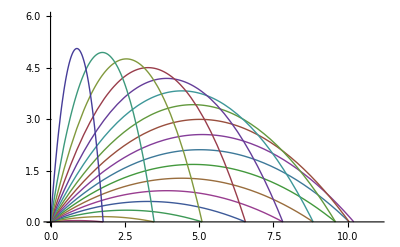

```mathematica
Plot[data, {x, 0, 11}, PlotRange->{0,6} ]
```